# Time Constant Calculator from Simulation Data

## Setup (automatically initialized when this notebook is opened)

### Function definitions

#### OrganizeWFData[fileName_,timeBounds_]

This function takes the filename of a waveform and extracts the coordinates of the waveform plot.  It also takes the timeBounds variable as input.  timeBounds is a variable that defines the start and stop times between which the data should be taken.

As output, this function returns a single data member which is organized as {axesLabel, d, numTaus}.

```mathematica
OrganizeWFDataMultTau[fileName_]:=Module[{axesLabel,d,numTaus,i},
i=Import[fileName,"Data"];
axesLabel=i⟦1⟧;
d=i⟦2;;⟧;
numTaus=Length[i⟦1⟧]-1;
Return[{axesLabel,d,numTaus}];
](* OrganizeWFDataMultTau Module *)
```

#### DataToPlotFormat[data_]

This function takes a data file and organizes it such that for each Ilk value, there is an independent xValue column corresponding to the yValue column

As output, this function returns a single data member which is organized as a list of sublists.  Each sublist corresponds to a different τ value and is comprised by a list of x,y coordinates that can be used to plot the data.

```mathematica
DataToPlotFormat[data_]:=Module[{organizedData},
organizedData=Transpose[data];
organizedData=Select[Transpose[{organizedData⟦1⟧,#}],NumberQ[#⟦2⟧]&]&/@organizedData⟦2;;⟧;
Return[organizedData];
](* DataToPlotFormat Module *)
```

### Ask user to select an input file with the waveform data

This section opens a system dialog box that asks the user to select a waveform file with the waveform trace.  It then sets the default working directory equal to the directory where this file is located.

```mathematica
fileName=SystemDialogInput["FileOpen","/home/noza/work/Mathematica/Scripts/LPFTimeConstantMeasurements", WindowTitle->"Select Simulation Waveform File (*.txt)"];
workingDir=DirectoryName[fileName];
SetDirectory[workingDir];
Print[Style["Working Directory:  ",FontFamily->"Helvetica", Bold] ,Style[Directory[],Italic]];
Print[Style["File Name: ", FontFamily->"Helvetica", Bold],FileNameTake[fileName]];
iInVal=ToExpression[Flatten[StringCases[fileName,"LPFWaveform_iin_"~~iIn:NumberString~~"_tau_sweep.txt"->iIn]]];
```

Working Directory:  /home/noza/work/Mathematica/Scripts/LPFTimeConstantMeasurements

File Name: LPFWaveform_iin_0.5_tau_sweep.txt

## Information Processing (Run-time)

### Process Waveform data from input file

This section takes the fileName gotten from the selection dialog and imports the data using the OrganizeWFData function defined in the functions section.  It then filters that data to the selected region, where the selected region specifies the data points that fit an exponential decay model.

```mathematica
timeBounds ={0.501,1.5};
AbsoluteTiming[{axesLabel,data,numTaus}=OrganizeWFDataMultTau[fileName]];(*Import data*)
(* Filter out data to get just the decay portion of the curve *)
timeFilteredData=Select[data,#⟦1⟧>timeBounds⟦1⟧&];
timeFilteredData=Select[timeFilteredData,#⟦1⟧<=timeBounds⟦2⟧&];
timeFilteredData=DataToPlotFormat[timeFilteredData];(*Organize data to allow it to be plottable*)
d=DataToPlotFormat[data];(*Organize data to allow it to be plottable*)
(* Extract tau values and labels from imported dataset *)
tauLabels=Rest[axesLabel];
tauVals=ToExpression[Flatten[StringCases[tauLabels,"i(vmeas_im):tau_"~~tau:NumberString~~"`"-> tau]]];
(* Take only positive current values as valid data *)
validTimeFilteredData=Select[#,#⟦2⟧>0&]&/@timeFilteredData;
(* Extract x-values from dataset *)
xValsExp=Transpose[#]⟦1⟧&/@validTimeFilteredData;
```

### Plot Data

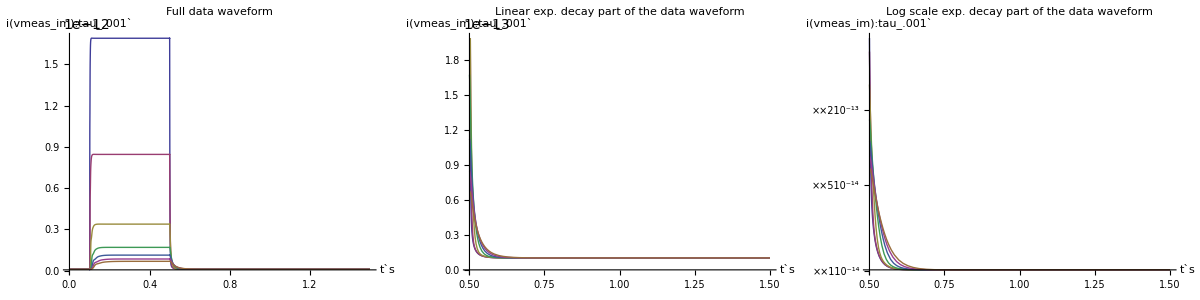
Data Waveforms
-Graphics-

```mathematica
imgSize=350;
Grid[{
{Text[Style["Data Waveforms",Bold,18]]},
{Grid[{
{ListLinePlot[d,AxesLabel->axesLabel,ImageSize->imgSize, PlotLabel->Style["Full data waveform",Bold],PlotRange->{Automatic,All}],
ListLinePlot[timeFilteredData,AxesLabel->axesLabel,ImageSize->imgSize, PlotLabel->Style["Linear exp. decay part of the data waveform",Bold]],
ListLogPlot[timeFilteredData,AxesLabel->axesLabel,Joined->True,ImageSize->imgSize, PlotLabel->Style["Log scale exp. decay part of the data waveform",Bold]]}
}]}
}]
```

### Manipulate Data

#### Calculate τ using exponential fit including offset

```mathematica
imgSize=500;
Manipulate[
(*plotNum=Sequence@@Flatten[Position[tauLabels,plotID]];*)
plotNum=Sequence@@Flatten[Position[tauVals,plotID]];
(* Select exponential range of data *)
selDataExp=Select[#,#⟦1⟧>lowerBoundExp&]&/@validTimeFilteredData;
selDataExp=Select[#,#⟦1⟧<upperBoundExp&]&/@selDataExp;
(* Shift the data so that the exponential curve is shifted left, such that the curve crosses the y-axis at the correct Isat value *)
selDataExp=Transpose[{#⟦;;,1⟧-lowerBoundExp,#⟦;;,2⟧}]&/@selDataExp;
(* Find the best fit *)
model=(a Exp[-t/τexp])+o;
fooCurveParams=FindFit[selDataExp⟦plotNum⟧,model,{a,{τexp,tauVals⟦plotNum⟧},{o,10^-14}},t,MaxIterations->10000];
fooCurve=Function[t,Evaluate[model/.fooCurveParams]];
fooCurveParamsAllTau=FindFit[#,model,{a,{τexp,tauVals⟦plotNum⟧},{o,10^-14}},t,MaxIterations->10000]&/@selDataExp;
fooCurveAllTau=Function[{t},Evaluate[model/.fooCurveParamsAllTau]];
currVals={a,o,τexp}/.fooCurveParams;
errTau=Abs[currVals⟦3⟧-tauVals⟦plotNum⟧];percErrTau=errTau/tauVals⟦plotNum⟧;
Grid[{
{Row[{Style["ι_in:  ",FontFamily->"Helvetica", Bold] ,Style[iInVal,Italic]}],Row[{Style["Curve Equation:  ",FontFamily->"Helvetica", Bold] ,Style[fooCurve,Italic]}]},
{Row[{Style["File Name:  ",FontFamily->"Helvetica", Bold] ,Style[FileNameTake[fileName],Italic]}],Row[{Style["Calculated τ:  ",FontFamily->"Helvetica", Bold] ,Style[currVals⟦3⟧,Italic]}]},
{Row[{Style["Measured Isat:  ",FontFamily->"Helvetica", Bold] ,Style[currVals⟦1⟧,Italic]}],Row[{Style["Δτ:  ",FontFamily->"Helvetica", Bold] ,Style[errTau,Italic]}]},
{Row[{Style["Measured offset:  ",FontFamily->"Helvetica", Bold] ,Style[currVals⟦2⟧,Italic]}],Row[{Style["τ_err(%):  ",FontFamily->"Helvetica", Bold] ,Style[percErrTau,Italic]}]},
{Row[{Style["Plot ID:  ",FontFamily->"Helvetica", Bold] ,Style[plotID,Italic]}],Row[{Style["Plot Number:  ",FontFamily->"Helvetica", Bold] ,Style[plotNum,Italic]}]},
{
Show[
Plot[fooCurveAllTau[t],{t,0,upperBoundExp-lowerBoundExp},ImageSize->imgSize,PlotRange->{{0,upperBoundExp-lowerBoundExp},{0,All}}],
Plot[fooCurve[t],{t,0,upperBoundExp-lowerBoundExp},ImageSize->imgSize,PlotStyle->Directive[Red,Thick],PlotRange->{{0,upperBoundExp-lowerBoundExp},{0,All}}]
],
Show[ListPlot[selDataExp⟦plotNum⟧,AxesLabel->axesLabel,ImageSize->imgSize,PlotStyle->Darker[Red],PlotRange->{{0,upperBoundExp-lowerBoundExp},{0,All}}],
Plot[fooCurve[t],{t,0,upperBoundExp-lowerBoundExp},ImageSize->imgSize,PlotRange->{{0,upperBoundExp-lowerBoundExp},{0,All}}]
]
},(*Middle Row of Grid*)
{
Show[
ListLinePlot[d,AxesLabel->axesLabel,ImageSize->imgSize, PlotLabel->Style["Full data waveform",Bold],PlotRange->{Automatic,All}],
ListLinePlot[d⟦plotNum⟧,AxesLabel->axesLabel,ImageSize->imgSize, PlotLabel->Style["Full data waveform",Bold],PlotRange->{Automatic,All},PlotStyle->Directive[Red,Thick]]
]
(*Heat Plot of errors for each tau value*)
}(*Bottom Row of Grid*)
}],
(*{{plotID,tauLabels⟦4⟧,"Plot ID"},tauLabels},*)
{{plotID,tauVals⟦1⟧,"Plot ID"},tauVals},
{{lowerBoundExp,xValsExp⟦plotNum⟧⟦10⟧,"Lower Bound"},Take[xValsExp⟦plotNum⟧,Min[20,Length[xValsExp⟦plotNum⟧]]],Appearance->{"Labeled","Open"}},
{{upperBoundExp,xValsExp⟦plotNum⟧⟦Floor[Length[Most[xValsExp⟦plotNum⟧]]/2]⟧,"Upper Bound"},Most[xValsExp⟦plotNum⟧]},LabelStyle->Medium, UnsavedVariables->{model,fooCurveParams, fooCurve,currVals,errTau,selDataExp,plotNum}
]
```

## Appendix

```mathematica
(*{
Show[
ListLinePlot[d,AxesLabel->axesLabel,ImageSize->imgSize, PlotLabel->Style["Full data waveform",Bold],PlotRange->{Automatic,All}],
ListLinePlot[d⟦plotNum⟧,AxesLabel->axesLabel,ImageSize->imgSize, PlotLabel->Style["Full data waveform",Bold],PlotRange->{Automatic,All},PlotStyle->Directive[Red,Thick]]
]
(*Heat Plot of errors for each tau value*)
}(*Bottom Row of Grid*)*)
```

### Calculate τ using linear fit of log of exponential decay (old method of doing this)

```mathematica
Manipulate[
dataBounds={lowerBound,upperBound};
selData=Select[timeFilteredData-offsetMin,#⟦2⟧>0&];
xVals=Transpose[selData]⟦1⟧;
logSelectedData=Transpose[{selData⟦;;,1⟧,Log[selData⟦;;,2⟧]}];
logSelData=Select[logSelectedData,#⟦1⟧>dataBounds⟦1⟧&];
logSelData=Select[logSelData,#⟦1⟧<dataBounds⟦2⟧&];
fooLine=Fit[logSelData,{1,t},t];
barLine=FindFit[logSelData,m t+b,{m,b},t];
τ=-1/m/.barLine;
Grid[{
{Row[{Style["Measured Isat:  ",FontFamily->"Helvetica", Bold] ,Style[Isat,Italic]}]},
{Row[{Style["Measured offset:  ",FontFamily->"Helvetica", Bold] ,Style[offsetMin,Italic]}]},
{Row[{Style["Calculated τ:  ",FontFamily->"Helvetica", Bold] ,Style[τ,Italic]}]},
{Show[ListPlot[logSelData,AxesLabel->axesLabel,ImageSize->imgSize,PlotStyle->Red],
ListLogPlot[selData,AxesLabel->axesLabel,ImageSize->imgSize],
Plot[fooLine,{t,0,0.7}]
]}
}],
{{lowerBound,0.501,"Lower Bound"},0.5,1.0,.001,Appearance->{"Labeled","Open"}},
{{upperBound,xVals⟦Floor[Length[xVals]/2]⟧,"Upper Bound"},xVals,Appearance->{"Labeled","Open"}}
]
```

### Playing with Exponents

#### Exponential without offset

0.1

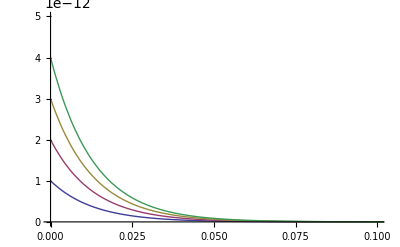

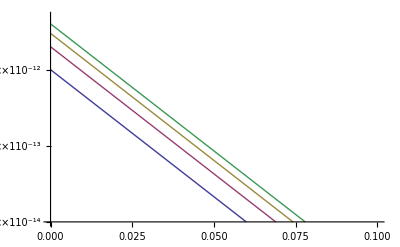

```mathematica
foo[a_,τtest_,t_]:=a*ⅇ^(-t/τtest);
a=100*10^-14;
τtest=0.013;
xMax=.1
Plot[{foo[a,τtest,t],foo[2 a,τtest,t],foo[3 a,τtest,t],foo[4 a,τtest,t]},{t,0,1.2},
PlotRange->{{0,xMax},{0,5 a}}]
LogPlot[{foo[a,τtest,t],foo[2 a,τtest,t],foo[3 a,τtest,t],foo[4 a,τtest,t]},{t,0,1.2},
PlotRange->{{0,xMax},{a/100,5 a}}]
```

#### Exponential with offset

0.05

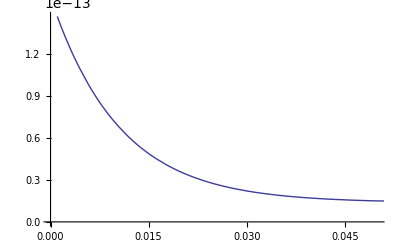

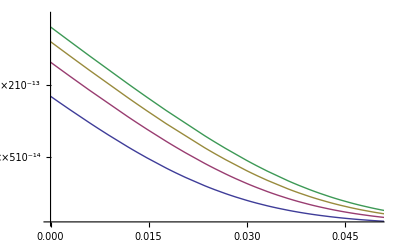

```mathematica
fooOff[a_,τtest_,t_,offset_]:=a*ⅇ^(-t/τtest)+offset;
atest=1.46548*10^-13;
τtest=0.0104876;
offsettest=1.36989*10^-14;
xMax=0.05
Plot[{fooOff[1 atest,τtest,t,offsettest]},{t,0,1.2},
PlotRange->{{0,xMax},{0,atest}}]
(*Plot[{fooOff[1 atest,τtest,t,offsettest],fooOff[2 atest,τtest,t,offsettest],fooOff[3 atest,τtest,t,offsettest],fooOff[4 atest,τtest,t,offsettest]},{t,0,1.2},
PlotRange->{{0,xMax},{0,5atest}}]*)
LogPlot[{fooOff[1 atest,τtest,t,offsettest],fooOff[2 atest,τtest,t,offsettest],fooOff[3 atest,τtest,t,offsettest],fooOff[4 atest,τtest,t,offsettest]},{t,0,1.2},
PlotRange->{{0,xMax},{atest/10,5atest}}]
```